# Comparison of methods for calculating coexistence mechanisms in a stochastic, discrete-time model. The Storage Effect features as a key coexistence mechanism.

Table 3 in the main text corresponds to s1=0.9. Table 2 in the main text corresponds to s1 = 0.5. Change the parameter value below to switch between the two versions of the model.

Here, the limiting factors are species densities. Instead of calculating coexistence mechanisms with a Taylor series about individual regulating factors F, we perform a taylor series about a synthetic competition parameter C (which is a linear combination of the regulating factors). Expanding with respect to the environmental and competition is conventional in MCT, but there are a couple additional benefits to this approach: 1) the code for calculating coexistence mechanisms is marginally simpler;  and 2) we can use the canonical method of selecting equilibrium parameters, which is to fix the equilibrium environmental parameter by letting the noise parameter go to zero, and then solve for the equilibrium competition parameter.  The scaling factors are still calculated using the matrix of sensitivities to individual limiting factors (variable name: PhiF).

```mathematica
(* ctrl+a to select all, then shift+enter to run the whole notebook *)
SeedRandom[20]
```

## Write Equations, select parameters, and simulate to make sure that species can coexist

```mathematica
(*equations for population density N and the environmental parameters ζ *)
N1tp1[{N1_,N2_,N3_,ζ1_,ζ2_,ζ3_}]:=N1 (Exp[ζ1]/(1+A[[1,1]] N1+A[[1,2]]N2+A[[1,3]] N3) +s1)
ζ1tp1[{N1_,N2_,N3_,ζ1_,ζ2_,ζ3_}]:=ρ1 ζ1 +Sqrt[1-ρ1^2]σ1 * RandomVariate[NormalDistribution[0,1]]
N2tp1[{N1_,N2_,N3_,ζ1_,ζ2_,ζ3_}]:=N2 (Exp[ζ2]/(1+A[[2,1]] N1+A[[2,2]]N2+A[[2,3]] N3) +s2)
ζ2tp1[{N1_,N2_,N3_,ζ1_,ζ2_,ζ3_}]:=ρ2 ζ2 +Sqrt[1-ρ2^2]σ2 * RandomVariate[NormalDistribution[0,1]]
N3tp1[{N1_,N2_,N3_,ζ1_,ζ2_,ζ3_}]:=N3(Exp[ζ3]/(1+A[[3,1]] N1+A[[3,2]]N2+A[[3,3]] N3) +s3)
ζ3tp1[{N1_,N2_,N3_,ζ1_,ζ2_,ζ3_}]:=ρ3 ζ3 +Sqrt[1-ρ3^2]σ3 * RandomVariate[NormalDistribution[0,1]]
```

```mathematica
(* set parameter values *)
(* matrix of competition coefficients *)
A = {
{1,0.01,0.01},
{0.01,1,0.10005},
{0.01,1.0001,1}
};

(* autocorrelation parameters *)
ρ1 = 0.0;ρ2 = 0.95;ρ3 = 0.95;
(* survival parameters *)
s1 = 0.9;s2 = 0.9;s3 = 0.9;
(* environmental fluctuation scales*)
σ1 = 0.5;σ2 = 0.5;σ3 = 0.5;
sVec ={s1,s2,s3}; (* vector of survival params, used to calculate speed conversion factors *)
```

{{-49.7512,50.2488},{50.2488,-49.7512}}

```mathematica
(* population map *)
f[{N1_,N2_,N3_,ζ1_,ζ2_,ζ3_}]:={
N1tp1[{N1,N2,N3,ζ1,ζ2,ζ3}],
N2tp1[{N1,N2,N3,ζ1,ζ2,ζ3}],
N3tp1[{N1,N2,N3,ζ1,ζ2,ζ3}],
ζ1tp1[{N1,N2,N3,ζ1,ζ2,ζ3}],
ζ2tp1[{N1,N2,N3,ζ1,ζ2,ζ3}],
ζ3tp1[{N1,N2,N3,ζ1,ζ2,ζ3}]}
```

```mathematica
(*simulation parameters*)
tMax=300000;
burnIn = 1000;
plotTMax =5000;
N1Init=0.1;
N2Init=0.1;
N3Init =0.1;
```

### Make sure that all species can coexist together

```mathematica
(* all species can coexist together *)
res=Transpose[NestList[f,{N1Init,N2Init, N3Init,0,0,0},plotTMax]];
```

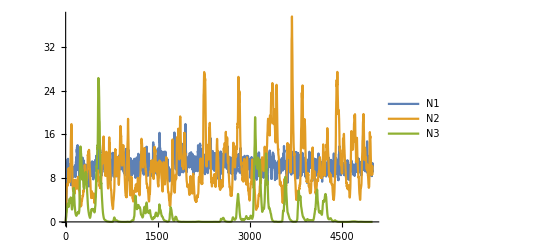

```mathematica
ListLinePlot[res[[1;;3,1;;plotTMax]],PlotLegends->{"N1","N2","N3"}]
```

```mathematica
(* average densities of species*)
CBarAll=Map[Mean[#]&, res[[1;;3]]]
(* variance of environmetnal parameter ζ *)
Map[Variance[#]&, res[[4;;6]]]
```

{10.2846,9.9967,1.71913}

{0.252844,0.248632,0.238009}

### Make sure that all pairs of species can coexist. This means that the mutual invasibility criterion is applicable.

#### Consumers 1 and 2

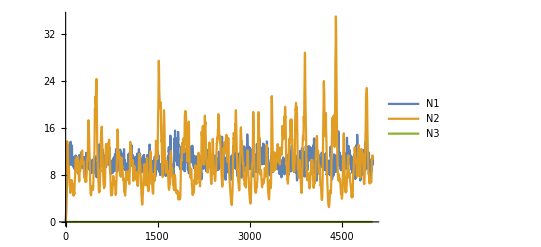

```mathematica
(* consumer 1 and 2 can coexist *)
res=Transpose[NestList[f,{N1Init,N2Init,0,0,0,0},plotTMax]];
ListLinePlot[res[[1;;3,1;;plotTMax]],PlotLegends->{"N1","N2","N3"}]
```

```mathematica
(* average densities of species*)
Map[Mean[#]&, res[[1;;3]]]
(* variance of environmetnal parameter ζ *)
Map[Variance[#]&, res[[4;;6]]]
```

{10.1085,10.0055,0.}

{0.242855,0.232864,0.266183}

#### Consumers 1 and 3

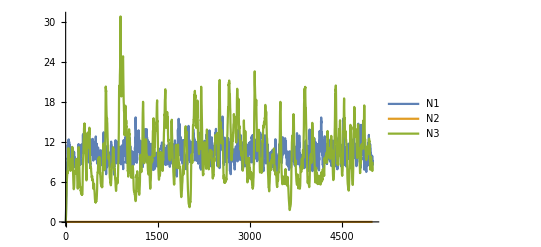

```mathematica
(* consumer 1 and 3 can coexist *)
res=Transpose[NestList[f,{N1Init,0,N3Init,0,0,0},plotTMax]];
ListLinePlot[res[[1;;3,1;;plotTMax]],PlotLegends->{"N1","N2","N3"}]
```

```mathematica
(* average densities of species*)
Map[Mean[#]&, res[[1;;3]]]
(* variance of environmetnal parameter ζ *)
Map[Variance[#]&, res[[4;;6]]]
```

{10.219,0.,10.1612}

{0.24876,0.258851,0.223381}

#### Consumers 2 and 3

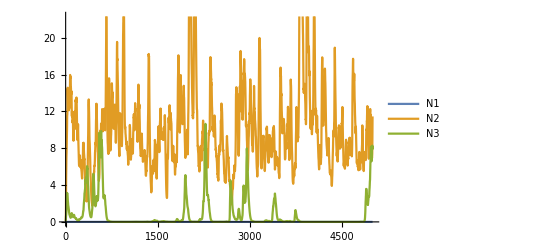

```mathematica
(* consumer 2 and 3 can coexist *)
res=Transpose[NestList[f,{0,N2Init,N3Init,0,0,0},plotTMax]];
ListLinePlot[res[[1;;3,1;;plotTMax]],PlotLegends->{"N1","N2","N3"}]
```

```mathematica
(* average densities of species*)
Map[Mean[#]&, res[[1;;3]]]
(* variance of environmetnal parameter ζ *)
Map[Variance[#]&, res[[4;;6]]]
```

{0.,10.0784,0.764715}

{0.254487,0.243355,0.267929}

## Get sensitivities to the determinants of the per-capita growth rate: Fix E at it’s temporal mean, 0, and then solve for the equilibrium competition parameter

```mathematica
λ[E_,C_,s_]:=( Exp[E]/(1+C) +s)
```

```mathematica
(* Fix the equilibrium competition at zero *)
EStar=ConstantArray[0,3];
CStar=ConstantArray[0,3];
```

```mathematica
(* solve for the equilbrium competition parameters *)
CStar[[1]]=C/.Solve[λ[EStar[[1]],C,s1] ==1,C][[1]]
CStar[[2]]=C/.Solve[λ[EStar[[2]],C,s2] ==1,C][[1]]
CStar[[3]]=C/.Solve[λ[EStar[[2]],C,s3] ==1,C][[1]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

9.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

9.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

9.

```mathematica
(* sensitivity to fluctutations in the environment *)
Alpha1= D[{Log[λ[E1,C1,s1]],Log[λ[E2,C2,s2]],Log[λ[E3,C3,s3]]},{{E1,E2,E3}}]/.{C1->CStar[[1]],C2->CStar[[2]],C3->CStar[[3]],E1->EStar[[1]],E2->EStar[[2]],E3->EStar[[3]]}//FullSimplify
```

{{0.1,0,0},{0,0.1,0},{0,0,0.1}}

```mathematica
(* sensitivity to fluctutations in competition *)
Phi=D[{Log[λ[E1,C1,s1]],Log[λ[E2,C2,s2]],Log[λ[E3,C3,s3]]},{{C1,C2,C3}}]/.{C1->CStar[[1]],C2->CStar[[2]],C3->CStar[[3]],E1->EStar[[1]],E2->EStar[[2]],E3->EStar[[3]]}//FullSimplify
```

{{-0.01,0,0},{0,-0.01,0},{0,0,-0.01}}

```mathematica
Phi//MatrixForm
```

(-0.01 | 0 | 0
0 | -0.01 | 0
0 | 0 | -0.01)

```mathematica
(* nonlinear responses to temporal variation in competition*)
Psi=D[{Log[λ[E1,C1,s1]],Log[λ[E2,C2,s2]],Log[λ[E3,C3,s3]]},{{C1,C2,C3}},{{C1,C2,C3}}]/.{C1->CStar[[1]],C2->CStar[[2]],C3->CStar[[3]],E1->EStar[[1]],E2->EStar[[2]],E3->EStar[[3]]}//FullSimplify
```

{{{0.0019,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0.0019,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0.0019}}}

```mathematica
Psi//MatrixForm
```

((0.0019
0
0) | (0
0
0) | (0
0
0)
(0
0
0) | (0
0.0019
0) | (0
0
0)
(0
0
0) | (0
0
0) | (0
0
0.0019))

```mathematica
(* nonlinear responses to temporal variation in the environment *)
Alpha2=D[{Log[λ[E1,C1,s1]],Log[λ[E2,C2,s2]],Log[λ[E3,C3,s3]]},{{E1,E2,E3}},{{E1,E2,E3}}]/.{C1->CStar[[1]],C2->CStar[[2]],C3->CStar[[3]],E1->EStar[[1]],E2->EStar[[2]],E3->EStar[[3]]}//FullSimplify
```

{{{0.09,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0.09,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0.09}}}

```mathematica
(* interaction effects for the product of fluctuations in the environmental parameter and the competition parameter *)
Theta = D[{Log[λ[E1,C1,s1]],Log[λ[E2,C2,s2]],Log[λ[E3,C3,s3]]},{{E1,E2,E3}},{{C1,C2,C3}}]/.{C1->CStar[[1]],C2->CStar[[2]],C3->CStar[[3]],E1->EStar[[1]],E2->EStar[[2]],E3->EStar[[3]]}//FullSimplify
```

{{{-0.009,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,-0.009,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,-0.009}}}

```mathematica
(* equilibrium values for individual limiting factors (i.e. species densities), keep EStar = 0 as the equilibrium environmental variable for each species *)
FStar=ConstantArray[0,{3,3}];
(* species 1 barely interact with species 2 or 3, so set species 1's equilibria for F2 and F3 to zero *)
FStar[[1,2]]=FStar[[1,3]]=0;
(* Solve for the equilibrium density of species 1 *)
FStar[[1,1]] =N1/.Solve[N1tp1[{N1,0,0,0,0,0}]/N1== 1, N1][[1]]; 
(* species 1 barely interact with species 2 or 3, so set species 2 and 3's equilibria for F1 to zero *)
FStar[[2,1]]=FStar[[3,1]]= 0;
(* solve for F2 and F3 within the subsystem of species 2 and 3 *)
FStar[[2,2]]=FStar[[3,2]] = N2/.Solve[{N2tp1[{0,N2,N3,0,0,0}]/N2== 1,N3tp1[{0,N2,N3,0,0,0}]/N3== 1},{N2,N3}][[1]];
FStar[[2,3]]=FStar[[3,3]] = N3/.Solve[{N2tp1[{0,N2,N3,0,0,0}]/N2== 1,N3tp1[{0,N2,N3,0,0,0}]/N3== 1},{N2,N3}][[1]];
FStar//MatrixForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

(9. | 0 | 0
0 | 9.0001 | -0.00100007
0 | 9.0001 | -0.00100007)

```mathematica
(* species responses to individual limiting factors -- used to calculate the scaling factors *)
prePhiF=D[{Log[N1tp1[{N1,N2,N3,0,0,0}]/N1],Log[N2tp1[{N1,N2,N3,0,0,0}]/N2],Log[N3tp1[{N1,N2,N3,0,0,0}]/N3]},{{N1,N2,N3}}]
```

{{-1/((0.9+1/(1+N1+0.01 N2+0.01 N3)) (1+N1+0.01 N2+0.01 N3)^2),-0.01/((0.9+1/(1+N1+0.01 N2+0.01 N3)) (1+N1+0.01 N2+0.01 N3)^2),-0.01/((0.9+1/(1+N1+0.01 N2+0.01 N3)) (1+N1+0.01 N2+0.01 N3)^2)},{-0.01/((0.9+1/(1+0.01 N1+N2+0.10005 N3)) (1+0.01 N1+N2+0.10005 N3)^2),-1/((0.9+1/(1+0.01 N1+N2+0.10005 N3)) (1+0.01 N1+N2+0.10005 N3)^2),-0.10005/((0.9+1/(1+0.01 N1+N2+0.10005 N3)) (1+0.01 N1+N2+0.10005 N3)^2)},{-0.01/((1+0.01 N1+1.0001 N2+N3)^2 (0.9+1/(1+0.01 N1+1.0001 N2+N3))),-1.0001/((1+0.01 N1+1.0001 N2+N3)^2 (0.9+1/(1+0.01 N1+1.0001 N2+N3))),-1/((1+0.01 N1+1.0001 N2+N3)^2 (0.9+1/(1+0.01 N1+1.0001 N2+N3)))}}

```mathematica
PhiF=Table[prePhiF[[i]]/.{N1->FStar[[i,1]],N2->FStar[[i,2]],N3->FStar[[i,3]]},{i,1,3}]//FullSimplify
```

{{-0.01,-0.0001,-0.0001},{-0.0001,-0.01,-0.0010005},{-0.0001,-0.010001,-0.01}}

```mathematica
PhiF//MatrixForm
```

(-0.01 | -0.0001 | -0.0001
-0.0001 | -0.01 | -0.0010005
-0.0001 | -0.010001 | -0.01)

## get intermediate quantities for invader-invader comparison- where all species are at typical densities

```mathematica
(* simulation parameters *)
N1Init=0.3;
N2Init=0.3;
N3Init =0.3;
plotTMax = 500;
```

```mathematica
res=Transpose[NestList[f,{N1Init,N2Init,N3Init,0,0,0},tMax]];
resT = Transpose[res];
```

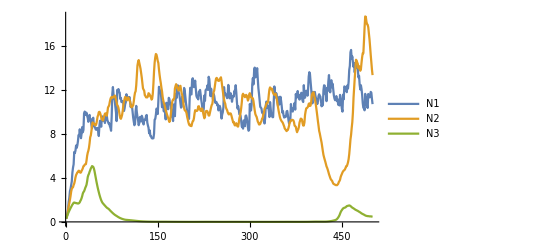

```mathematica
ListLinePlot[res[[1;;3,1;;plotTMax]],PlotLegends->{"N1","N2","N3"}]
```

```mathematica
FVecs = res[[1;;3,burnIn;;tMax]]//Transpose;
(* temporal average of species densities *)
FBarHigh=Mean[FVecs];
CVecs = Table[A[[j,1]]*res[[1,i]]+A[[j,2]]*res[[2,i]]+A[[j,3]]*res[[3,i]],{i,burnIn,tMax},{j,1,3}];
EVecs = Table[res[[j,i]],{i,burnIn,tMax},{j,4,6}];
(* temporal average of the competition parameters *)
CBarHigh=Mean[CVecs];
(* temporal average of the environmental parameters *)
EBarHigh=Map[Mean[#[[burnIn;;tMax]]]&, res[[4;;6]]];
(* temporal variance of the competition parameter *)
CVarHigh=Table[Covariance[CVecs[[;;,i]],CVecs [[;;,j]]],{i,1,3},{j,1,3}];
(* temporal variance of the environmental parameter *)
EVarHigh=Table[Covariance[EVecs[[;;,i]],EVecs [[;;,j]]],{i,1,3},{j,1,3}];
(* temporal covariance between the environment and competition *)
CECovHigh=Table[Covariance[CVecs[[;;,i]],EVecs [[;;,j]]],{i,1,3},{j,1,3}];
```

```mathematica
(* long-term average per-capita growth rate of each species *)
avgGRHigh=Mean[Table[Log[λ[EVecs[[i,j]],CVecs[[i,j]],sVec[[j]]]],{i,1,tMax-burnIn},{j,1,3}]]
(* long-term average per-capita growth rate of each species, calculated while holding fixing the competition parameter at its equilibrium value *)
avgGRCStarHigh=Mean[Table[Log[λ[EVecs[[i,j]],CStar[[j]],sVec[[j]]]],{i,1,tMax-burnIn},{j,1,3}]]
(* long-term average per-capita growth rate of each species, calculated while holding fixing the environmental parameter at its equilibrium value *)
avgGREStarHigh=Mean[Table[Log[λ[EStar[[j]],CVecs[[i,j]],sVec[[j]]]],{i,1,tMax-burnIn},{j,1,3}]]
(* long-term average per-capita growth rate of each species, calculated while holding fixing the environmental parameter at its equilibrium value, and the competition parameter at its temporal average *)
avgGREStarCBarHigh=Mean[Table[Log[λ[EStar[[j]],CBarHigh[[j]],sVec[[j]]]],{i,1,tMax-burnIn},{j,1,3}]]
```

{-8.72252×10^-9,-8.01315×10^-7,-4.3797×10^-6}

{0.0113884,0.0120264,0.0102483}

{-0.010437,0.00220678,-0.00728251}

{-0.011554,-0.0121091,-0.0195158}

## Invasion analysis: species 1 is the invader

```mathematica
(* simulation parameters *)
N1Init=0;
N2Init=0.3;
N3Init =0.3;
plotTMax = 500;
```

#### Consumers 2 and 3

```mathematica
(* consumer 2 and 3 can coexist *)
res=Transpose[NestList[f,{N1Init,N2Init,N3Init,0,0,0},tMax]];
resT = Transpose[res];
```

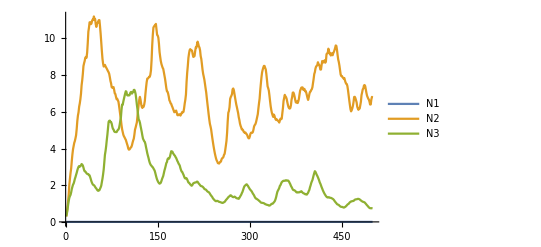

```mathematica
ListLinePlot[res[[1;;3,1;;plotTMax]],PlotLegends->{"N1","N2","N3"}]
```

```mathematica
FVecs = res[[1;;3,burnIn;;tMax]]//Transpose;
(* temporal average of species densities *)
FBar1=Mean[FVecs];
CVecs = Table[A[[j,1]]*res[[1,i]]+A[[j,2]]*res[[2,i]]+A[[j,3]]*res[[3,i]],{i,burnIn,tMax},{j,1,3}];
EVecs = Table[res[[j,i]],{i,burnIn,tMax},{j,4,6}];
(* temporal average of the competition parameters *)
CBar1=Mean[CVecs];
(* temporal average of the environmental parameters *)
EBar1=Map[Mean[#[[burnIn;;tMax]]]&, res[[4;;6]]];
(* temporal variance of the competition parameter *)
CVar1=Table[Covariance[CVecs[[;;,i]],CVecs [[;;,j]]],{i,1,3},{j,1,3}];
(* temporal variance of the environmental parameter *)
EVar1=Table[Covariance[EVecs[[;;,i]],EVecs [[;;,j]]],{i,1,3},{j,1,3}];
(* temporal covariance between the environment and competition *)
CECov1=Table[Covariance[CVecs[[;;,i]],EVecs [[;;,j]]],{i,1,3},{j,1,3}];
```

```mathematica
(* long-term average per-capita growth rate of each species *)
avgGR1=Mean[Table[Log[λ[EVecs[[i,j]],CVecs[[i,j]],sVec[[j]]]],{i,1,tMax-burnIn},{j,1,3}]]
(* long-term average per-capita growth rate of each species, calculated while holding fixing the competition parameter at its equilibrium value *)
avgGRCStar1=Mean[Table[Log[λ[EVecs[[i,j]],CStar[[j]],sVec[[j]]]],{i,1,tMax-burnIn},{j,1,3}]]
(* long-term average per-capita growth rate of each species, calculated while holding fixing the environmental parameter at its equilibrium value *)
avgGREStar1=Mean[Table[Log[λ[EStar[[j]],CVecs[[i,j]],sVec[[j]]]],{i,1,tMax-burnIn},{j,1,3}]]
(* long-term average per-capita growth rate of each species, calculated while holding fixing the environmental parameter at its equilibrium value, and the competition parameter at its temporal average *)
avgGREStarCBar1=Mean[Table[Log[λ[EStar[[j]],CBar1[[j]],sVec[[j]]]],{i,1,tMax-burnIn},{j,1,3}]]
```

{0.617221,7.72604×10^-7,-0.0000198284}

{0.011617,0.0118986,0.0114978}

{0.586713,0.00275189,-0.00795065}

{0.585961,-0.0120508,-0.0203264}

```mathematica
(* scaling factors *)
preQ = Drop[PhiF[[1]],{1}].PseudoInverse[Drop[PhiF,{1},{1}]];
q1 = Insert[-preQ,1,1]//N
(* the simple comparison *)
noQ1 = {1,-1/2,-1/2}//N
(* speed conversion factors, "generation time" method *)
SCF1= {1,-(1-s1)/(2(1-s2)),-(1-s1)/(2(1-s2))}//N
(* speed conversion factors, "universal method": the speed parameter is the total of all sensitivities to the determinants of per-capita growth*)
preSCF =Total[Abs[Alpha1],{2}]+Total[Abs[Phi],{2}] +Total[Abs[Psi],{2,3}] + Total[Abs[Alpha2],{2,3}]+Total[Abs[Theta],{2,3}];
preSCF2 = preSCF[[1]]/preSCF/2;
SCF1Alt= Insert[-Drop[preSCF2,{1}] ,1,1]//N
```

{1.,1.11119×10^-6,-0.0100001}

{1.,-0.5,-0.5}

{1.,-0.5,-0.5}

{1.,-0.5,-0.5}

```mathematica
Drop[PhiF[[1]],{1}]
```

{-0.0001,-0.0001}

```mathematica
PseudoInverse[Drop[PhiF,{1},{1}]]
```

{{-111.119,11.1174},{111.13,-111.119}}

```mathematica
Total[PseudoInverse[Drop[PhiF,{1},{1}]],{2}]
```

{-100.001,0.0111119}

## Invasion analysis: species 2 is the invader

```mathematica
(* simulation parameters *)
N1Init=0.3;
N2Init=0;
N3Init =0.3;
plotTMax = 500;
```

#### Consumers 1 and 3

```mathematica
(* consumer 1 and 3 can coexist *)
res=Transpose[NestList[f,{N1Init,N2Init,N3Init,0,0,0},tMax]];
resT = Transpose[res];
```

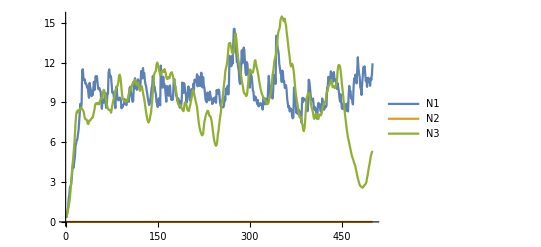

```mathematica
ListLinePlot[res[[1;;3,1;;plotTMax]],PlotLegends->{"N1","N2","N3"}]
```

```mathematica
FVecs = res[[1;;3,burnIn;;tMax]]//Transpose;
(* temporal average of species densities *)
FBar2=Mean[FVecs];
CVecs = Table[A[[j,1]]*res[[1,i]]+A[[j,2]]*res[[2,i]]+A[[j,3]]*res[[3,i]],{i,burnIn,tMax},{j,1,3}];
EVecs = Table[res[[j,i]],{i,burnIn,tMax},{j,4,6}];
(* temporal average of the competition parameters *)
CBar2=Mean[CVecs];
(* temporal average of the environmental parameters *)
EBar2=Map[Mean[#[[burnIn;;tMax]]]&, res[[4;;6]]];
(* temporal variance of the competition parameter *)
CVar2=Table[Covariance[CVecs[[;;,i]],CVecs [[;;,j]]],{i,1,3},{j,1,3}];
(* temporal variance of the environmental parameter *)
EVar2=Table[Covariance[EVecs[[;;,i]],EVecs [[;;,j]]],{i,1,3},{j,1,3}];
(* temporal covariance between the environment and competition *)
CECov2=Table[Covariance[CVecs[[;;,i]],EVecs [[;;,j]]],{i,1,3},{j,1,3}];
```

```mathematica
(* long-term average per-capita growth rate of each species *)
avgGR2=Mean[Table[Log[λ[EVecs[[i,j]],CVecs[[i,j]],sVec[[j]]]],{i,1,tMax-burnIn},{j,1,3}]]
(* long-term average per-capita growth rate of each species, calculated while holding fixing the competition parameter at its equilibrium value *)
avgGRCStar2=Mean[Table[Log[λ[EVecs[[i,j]],CStar[[j]],sVec[[j]]]],{i,1,tMax-burnIn},{j,1,3}]]
(* long-term average per-capita growth rate of each species, calculated while holding fixing the environmental parameter at its equilibrium value *)
avgGREStar2=Mean[Table[Log[λ[EStar[[j]],CVecs[[i,j]],sVec[[j]]]],{i,1,tMax-burnIn},{j,1,3}]]
(* long-term average per-capita growth rate of each species, calculated while holding fixing the environmental parameter at its equilibrium value, and the competition parameter at its temporal average *)
avgGREStarCBar2=Mean[Table[Log[λ[EStar[[j]],CBar2[[j]],sVec[[j]]]],{i,1,tMax-burnIn},{j,1,3}]]
```

{-2.64299×10^-7,0.354866,1.96378×10^-6}

{0.0114212,0.0112591,0.0114645}

{-0.0104585,0.328215,0.00299413}

{-0.0115807,0.31537,-0.011721}

```mathematica
(* scaling factors *)
preQ = Drop[PhiF[[2]],{2}].PseudoInverse[Drop[PhiF,{2},{2}]];
q2 = Insert[-preQ,1,2]//N
(* the simple comparison *)
noQ2 = {-1/2,1,-1/2}//N
(* speed conversion factors, "generation time" method *)
SCF2= {-(1-s2)/(2(1-s1)),1,-(1-s2)/(2(1-s3))}//N
(* speed conversion factors, "universal method": the speed parameter is the total of all sensitivities to the determinants of per-capita growth*)
preSCF =Total[Abs[Alpha1],{2}]+Total[Abs[Phi],{2}] +Total[Abs[Psi],{2,3}] + Total[Abs[Alpha2],{2,3}]+Total[Abs[Theta],{2,3}];
preSCF2 = preSCF[[2]]/preSCF/2;
SCF2Alt= Insert[-Drop[preSCF2,{2}] ,1,2]//N
```

{-0.0090004,1.,-0.09996}

{-0.5,1.,-0.5}

{-0.5,1.,-0.5}

{-0.5,1.,-0.5}

## Invasion analysis: species 3 is the invader

```mathematica
(* simulation parameters *)
N1Init=0.3;
N2Init=0.3;
N3Init =0;
plotTMax = 500;
```

#### Consumers 1 and 3

```mathematica
(* consumer 2 and 3 can coexist *)
res=Transpose[NestList[f,{N1Init,N2Init,N3Init,0,0,0},tMax]];
resT = Transpose[res];
```

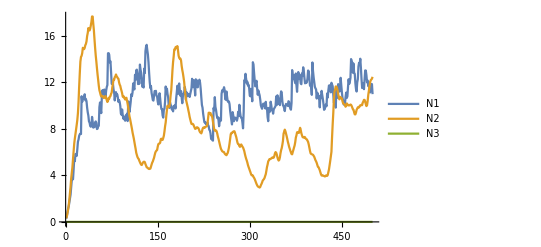

```mathematica
ListLinePlot[res[[1;;3,1;;plotTMax]],PlotLegends->{"N1","N2","N3"}]
```

```mathematica
FVecs = res[[1;;3,burnIn;;tMax]]//Transpose;
(* temporal average of species densities *)
FBar3=Mean[FVecs];
CVecs = Table[A[[j,1]]*res[[1,i]]+A[[j,2]]*res[[2,i]]+A[[j,3]]*res[[3,i]],{i,burnIn,tMax},{j,1,3}];
EVecs = Table[res[[j,i]],{i,burnIn,tMax},{j,4,6}];
(* temporal average of the competition parameters *)
CBar3=Mean[CVecs];
(* temporal average of the environmental parameters *)
EBar3=Map[Mean[#[[burnIn;;tMax]]]&, res[[4;;6]]];
(* temporal variance of the competition parameter *)
CVar3=Table[Covariance[CVecs[[;;,i]],CVecs [[;;,j]]],{i,1,3},{j,1,3}];
(* temporal variance of the environmental parameter *)
EVar3=Table[Covariance[EVecs[[;;,i]],EVecs [[;;,j]]],{i,1,3},{j,1,3}];
(* temporal covariance between the environment and competition *)
CECov3=Table[Covariance[CVecs[[;;,i]],EVecs [[;;,j]]],{i,1,3},{j,1,3}];
```

```mathematica
(* long-term average per-capita growth rate of each species *)
avgGR3=Mean[Table[Log[λ[EVecs[[i,j]],CVecs[[i,j]],sVec[[j]]]],{i,1,tMax-burnIn},{j,1,3}]]
(* long-term average per-capita growth rate of each species, calculated while holding fixing the competition parameter at its equilibrium value *)
avgGRCStar3=Mean[Table[Log[λ[EVecs[[i,j]],CStar[[j]],sVec[[j]]]],{i,1,tMax-burnIn},{j,1,3}]]
(* long-term average per-capita growth rate of each species, calculated while holding fixing the environmental parameter at its equilibrium value *)
avgGREStar3=Mean[Table[Log[λ[EStar[[j]],CVecs[[i,j]],sVec[[j]]]],{i,1,tMax-burnIn},{j,1,3}]]
(* long-term average per-capita growth rate of each species, calculated while holding fixing the environmental parameter at its equilibrium value, and the competition parameter at its temporal average *)
avgGREStarCBar3=Mean[Table[Log[λ[EStar[[j]],CBar3[[j]],sVec[[j]]]],{i,1,tMax-burnIn},{j,1,3}]]
```

{-4.16637×10^-7,1.41431×10^-6,0.0138476}

{0.0114336,0.0121348,0.0118343}

{-0.010487,0.0021984,0.0021896}

{-0.0115949,-0.0122427,-0.0122507}

```mathematica
(* scaling factors *)
preQ = Drop[PhiF[[3]],{3}].PseudoInverse[Drop[PhiF,{3},{3}]];
q3= Insert[-preQ,1,3]//N
(* the simple comparison *)
noQ3 = {-1/2,-1/2,1}//N
(* speed conversion factors, "generation time" method *)
SCF3= {-(1-s3)/(2(1-s1)),-(1-s3)/(2(1-s2)),1}//N
(* speed conversion factors, "universal method": the speed parameter is the total of all sensitivities to the determinants of per-capita growth *)
preSCF =Total[Abs[Alpha1],{2}]+Total[Abs[Phi],{2}] +Total[Abs[Psi],{2,3}] + Total[Abs[Alpha2],{2,3}]+Total[Abs[Theta],{2,3}];
preSCF2 = preSCF[[3]]/preSCF/2;
SCF3Alt= Insert[-Drop[preSCF2,{3}] ,1,3]//N
```

{1.0001×10^-6,-1.0001,1.}

{-0.5,-0.5,1.}

{-0.5,-0.5,1.}

{-0.5,-0.5,1.}

```mathematica
PseudoInverse[Drop[PhiF,{3},{3}]]
```

{{-100.01,1.0001},{1.0001,-100.01}}

## Functions for computing coexistence mechansisms

### Invader-resident comparisons

#### small-noise

```mathematica
(* regular small-noise coexistence mechanisms - used with the scaling factors *)
rPrime[q_,Alpha1_,Alpha2_, Phi_,EBar_,EVar_,EStar_, CStar_]:=q.(Alpha1.(EBar -EStar) +(1/2)Table[Total[ Alpha2[[i]]*EVar,{1,2}],{i,1,3}]-Total[Phi*CStar ,{2}])

deltaRho[q_, Phi_, CBar_]:=q.Phi.CBar
deltaRhoF[q_, PhiF_, FBar_]:=q.PhiF.FBar

deltaN[q_, Psi_, CVar_]:=(1/2)q.Table[Total[Psi[[i]]*CVar,{1,2}],{i,1,3}]
deltaI[q_, Theta_, CECov_]:=(1/2)q.Table[Total[Theta[[i]]*CECov,{1,2}],{i,1,3}]

(* new small-noise coexistence mechanisms - CStar is not shunted to rPrime - used with the simple average and speed conversion factors *)

deltaENew[q_,Alpha1_,Alpha2_, Phi_,EBar_,EVar_,EStar_, CStar_]:=q.(Alpha1.(EBar -EStar) +(1/2)Table[Total[ Alpha2[[i]]*EVar,{1,2}],{i,1,3}])

deltaRhoNew[q_, Phi_, CBar_,CStar_]:=q.Phi.CBar - q.Total[Phi*CStar ,{2}]
deltaRhoFNew[q_, PhiF_, FBar_,FStar_]:=q.PhiF.FBar - q.Total[PhiF*FStar ,{2}]

deltaNNew[q_, Psi_, CVar_]:=(1/2)q.Table[Total[Psi[[i]]*CVar,{1,2}],{i,1,3}]
deltaINew[q_, Theta_, CECov_]:=(1/2)q.Table[Total[Theta[[i]]*CECov,{1,2}],{i,1,3}]
```

#### exact

```mathematica
(* regular exact coexistence mechansism - used with scaling factors *)
deltaEE[q_, avgGRCStar_]:=q.(avgGRCStar)
rPrimeE[q_, avgGRCStar_, avgGREStarCBar_ ,Phi_, CStar_]:=q.(avgGRCStar)- q.Total[Phi*CStar ,{2}]
rPrimeE[q_, avgGRCStar_, avgGREStarCBar_]:=q.(avgGRCStar)+q.(avgGREStarCBar)
deltaRhoE[q_, avgGREStarCBar_,Phi_, CStar_]:=q.(avgGREStarCBar)+ q.Total[Phi*CStar ,{2}]
deltaRhoE[q_, avgGREStarCBar_,Phi_, CStar_]:=0
deltaRhoENew[q_, avgGREStarCBar_]:=q.(avgGREStarCBar)
deltaNE[q_,avgGREStar_,avgGREStarCBar_]:=q.(avgGREStar-avgGREStarCBar)
deltaIE[q_,avgGREStar_,avgGRCStar_,avgGR_]:=q.(avgGR-avgGREStar-avgGRCStar)
```

### Invader-invader comparisons

```mathematica
(* new small-noise coexistence mechanisms - CStar is not shunted to rPrime - used with the simple average and speed conversion factors *)
deltaRhoNewII[Phi_, CBarLow_, CBarHigh_, spInd_]:=Phi[[spInd,;;]].(CBarLow-CBarHigh)
deltaNNewII[Psi_, CVarLow_, CVarHigh_, spInd_]:=(1/2)*Total[Psi[[spInd]]*(CVarLow-CVarHigh),{1,2}]
deltaINewII[Theta_, CECovLow_, CECovHigh_, spInd_]:=(1/2)*Total[Theta[[spInd]]*(CECovLow-CECovHigh),{1,2}]
```

#### exact

```mathematica
(* regular exact coexistence mechansism - used with scaling factors *)
deltaEEII[ avgGRCStarLow_, avgGRCStarHigh_, spInd_]:=(avgGRCStarLow[[spInd]])-(avgGRCStarHigh[[spInd]])
deltaRhoEII[avgGREStarCBarLow_,avgGREStarCBarHigh_, spInd_]:=(avgGREStarCBarLow[[spInd]])-(avgGREStarCBarHigh[[spInd]])
deltaNEII[avgGREStarLow_,avgGREStarCBarLow_,avgGREStarHigh_,avgGREStarCBarHigh_, spInd_]:=(avgGREStarLow[[spInd]]-avgGREStarCBarLow[[spInd]])-(avgGREStarHigh[[spInd]]-avgGREStarCBarHigh[[spInd]])
deltaIEII[avgGREStarLow_,avgGRCStarLow_,avgGRLow_,avgGREStarHigh_,avgGRCStarHigh_,avgGRHigh_, spInd_]:=(avgGRLow[[spInd]]-avgGREStarLow[[spInd]]-avgGRCStarLow[[spInd]])-(avgGRHigh[[spInd]]-avgGREStarHigh[[spInd]]-avgGRCStarHigh[[spInd]])
```

## Tables

```mathematica
q1
```

{1.,1.11119×10^-6,-0.0100001}

```mathematica
names = {rPrime,Δρ,ΔN,ΔI,rPrime^(e),Δρ^(e),ΔN^(e),ΔI^(e),invGR, invGRv2^(e), invGR^(e)};
spInd = 1;
T1={{rPrime[q1,Alpha1,Alpha2, Phi,EBar1,EVar1, EStar, CStar], deltaRho[q1, Phi, CBar1], deltaN[q1, Psi, CVar1],deltaI[q1,Theta, CECov1],
 rPrimeE[q1,  avgGRCStar1, avgGREStarCBar1],deltaRhoE[q1, avgGREStarCBar1,Phi, CStar],deltaNE[q1,avgGREStar1,avgGREStarCBar1],deltaIE[q1,avgGREStar1,avgGRCStar1,avgGR1],
rPrime[q1,Alpha1,Alpha2, Phi,EBar1,EVar1, EStar, CStar]+ deltaRho[q1, Phi, CBar1]+ deltaN[q1, Psi, CVar1]+deltaI[q1,Theta, CECov1],
 rPrimeE[q1,  avgGRCStar1, avgGREStarCBar1]+deltaRhoE[q1, avgGREStarCBar1,Phi, CStar]+deltaNE[q1,avgGREStar1,avgGREStarCBar1]+deltaIE[q1,avgGREStar1,avgGRCStar1,avgGR1],avgGR1[[spInd]] },

{deltaENew[noQ1,Alpha1,Alpha2, Phi,EBar1,EVar1, EStar, CStar], deltaRhoNew[noQ1, Phi, CBar1,CStar], deltaNNew[noQ1, Psi, CVar1],deltaINew[noQ1,Theta, CECov1],
 deltaEE[noQ1, avgGRCStar1],deltaRhoENew[noQ1, avgGREStarCBar1],deltaNE[noQ1,avgGREStar1,avgGREStarCBar1],deltaIE[noQ1,avgGREStar1,avgGRCStar1,avgGR1],
deltaENew[noQ1,Alpha1,Alpha2, Phi,EBar1,EVar1, EStar, CStar]+ deltaRhoNew[noQ1, Phi, CBar1,CStar]+ deltaNNew[noQ1, Psi, CVar1]+deltaINew[noQ1,Theta, CECov1],
 deltaEE[noQ1, avgGRCStar1]+deltaRhoENew[noQ1, avgGREStarCBar1]+deltaNE[noQ1,avgGREStar1,avgGREStarCBar1]+deltaIE[noQ1,avgGREStar1,avgGRCStar1,avgGR1],
avgGR1[[spInd]] },

{deltaENew[SCF1,Alpha1,Alpha2, Phi,EBar1,EVar1, EStar, CStar], deltaRhoNew[SCF1, Phi, CBar1,CStar], deltaNNew[SCF1, Psi, CVar1],deltaINew[SCF1,Theta, CECov1],
 deltaEE[SCF1, avgGRCStar1],deltaRhoENew[SCF1, avgGREStarCBar1],deltaNE[SCF1,avgGREStar1,avgGREStarCBar1],deltaIE[SCF1,avgGREStar1,avgGRCStar1,avgGR1],
deltaENew[SCF1,Alpha1,Alpha2, Phi,EBar1,EVar1, EStar, CStar]+ deltaRhoNew[SCF1, Phi, CBar1,CStar]+ deltaNNew[SCF1, Psi, CVar1]+deltaINew[SCF1,Theta, CECov1],
 deltaEE[SCF1, avgGRCStar1]+deltaRhoENew[SCF1, avgGREStarCBar1]+deltaNE[SCF1,avgGREStar1,avgGREStarCBar1]+deltaIE[SCF1,avgGREStar1,avgGRCStar1,avgGR1],
avgGR1[[spInd]] },

{deltaENew[SCF1Alt,Alpha1,Alpha2, Phi,EBar1,EVar1, EStar, CStar], deltaRhoNew[SCF1Alt, Phi, CBar1,CStar], deltaNNew[SCF1Alt, Psi, CVar1],deltaINew[SCF1Alt,Theta, CECov1],
 deltaEE[SCF1Alt, avgGRCStar1],deltaRhoENew[SCF1Alt, avgGREStarCBar1],deltaNE[SCF1Alt,avgGREStar1,avgGREStarCBar1],deltaIE[SCF1Alt,avgGREStar1,avgGRCStar1,avgGR1],
deltaENew[SCF1Alt,Alpha1,Alpha2, Phi,EBar1,EVar1, EStar, CStar]+ deltaRhoNew[SCF1Alt, Phi, CBar1,CStar]+ deltaNNew[SCF1Alt, Psi, CVar1]+deltaINew[SCF1Alt,Theta, CECov1],
 deltaEE[SCF1Alt, avgGRCStar1]+deltaRhoENew[SCF1Alt, avgGREStarCBar1]+deltaNE[SCF1Alt,avgGREStar1,avgGREStarCBar1]+deltaIE[SCF1Alt,avgGREStar1,avgGRCStar1,avgGR1],
avgGR1[[spInd]] },

{0, deltaRhoNewII[Phi, CBar1, CBarHigh, spInd],deltaNNewII[Psi, CVar1, CVarHigh, spInd],deltaINewII[Theta, CECov1, CECovHigh, spInd],
deltaEEII[ avgGRCStar1, avgGRCStarHigh, spInd],deltaRhoEII[avgGREStarCBar1,avgGREStarCBarHigh, spInd],deltaNEII[avgGREStar1,avgGREStarCBar1,avgGREStarHigh,avgGREStarCBarHigh, spInd],deltaIEII[avgGREStar1,avgGRCStar1,avgGR1,avgGREStarHigh,avgGRCStarHigh,avgGRHigh, spInd],
0+ deltaRhoNewII[Phi, CBar1, CBarHigh, spInd]+deltaNNewII[Psi, CVar1, CVarHigh, spInd]+deltaINewII[Theta, CECov1, CECovHigh, spInd],
deltaEEII[ avgGRCStar1, avgGRCStarHigh, spInd]+deltaRhoEII[avgGREStarCBar1,avgGREStarCBarHigh, spInd]+deltaNEII[avgGREStar1,avgGREStarCBar1,avgGREStarHigh,avgGREStarCBarHigh, spInd]+deltaIEII[avgGREStar1,avgGRCStar1,avgGR1,avgGREStarHigh,avgGRCStarHigh,avgGRHigh, spInd],
avgGR1[[spInd]] }};
NumberForm[MatrixForm[Prepend[T1,names]],{3,4}]
```

(rPrime | Δρ | ΔN | ΔI | rPrime^e | Δρ^e | ΔN^e | ΔI^e | invGR | invGRv2^e | invGR^e
0.1000 | 4.3400×10^-19 | -0.0002 | 0.0000 | 0.5980 | 0 | 0.0006 | 0.0189 | 0.1000 | 0.6170 | 0.6170
-0.0000 | 0.1080 | -0.0239 | 0.0051 | -0.0001 | 0.6020 | -0.0128 | 0.0280 | 0.0893 | 0.6170 | 0.6170
-0.0000 | 0.1080 | -0.0239 | 0.0051 | -0.0001 | 0.6020 | -0.0128 | 0.0280 | 0.0893 | 0.6170 | 0.6170
-0.0000 | 0.1080 | -0.0239 | 0.0051 | -0.0001 | 0.6020 | -0.0128 | 0.0280 | 0.0893 | 0.6170 | 0.6170
0 | 0.1020 | -0.0016 | -8.1900×10^-7 | 0.0002 | 0.5980 | -0.0004 | 0.0198 | 0.1000 | 0.6170 | 0.6170)

```mathematica
names = {rPrime,Δρ,ΔN,ΔI,rPrime^(e),Δρ^(e),ΔN^(e),ΔI^(e),invGR, invGR^(e)};
spInd = 2;
T2={{rPrime[q2,Alpha1,Alpha2, Phi,EBar2,EVar2, EStar, CStar], deltaRho[q2, Phi, CBar2], deltaN[q2, Psi, CVar2],deltaI[q2,Theta, CECov2],
  rPrimeE[q2,  avgGRCStar2, avgGREStarCBar2],deltaRhoE[q2, avgGREStarCBar2,Phi, CStar],deltaNE[q2,avgGREStar2,avgGREStarCBar2],deltaIE[q2,avgGREStar2,avgGRCStar2,avgGR2],
rPrime[q2,Alpha1,Alpha2, Phi,EBar2,EVar2, EStar, CStar]+ deltaRho[q2, Phi, CBar2]+ deltaN[q2, Psi, CVar2]+deltaI[q2,Theta, CECov2],avgGR2[[spInd]] },

{deltaENew[noQ2,Alpha1,Alpha2, Phi,EBar2,EVar2, EStar, CStar], deltaRhoNew[noQ2, Phi, CBar2,CStar], deltaNNew[noQ2, Psi, CVar2],deltaINew[noQ2,Theta, CECov2],
 deltaEE[noQ2, avgGRCStar2],deltaRhoENew[noQ2, avgGREStarCBar2],deltaNE[noQ2,avgGREStar2,avgGREStarCBar2],deltaIE[noQ2,avgGREStar2,avgGRCStar2,avgGR2],
deltaENew[noQ2,Alpha1,Alpha2, Phi,EBar2,EVar2, EStar, CStar]+ deltaRhoNew[noQ2, Phi, CBar2,CStar]+ deltaNNew[noQ2, Psi, CVar2]+deltaINew[noQ2,Theta, CECov2],avgGR2[[spInd]] },

{deltaENew[SCF2,Alpha1,Alpha2, Phi,EBar2,EVar2, EStar, CStar], deltaRhoNew[SCF2, Phi, CBar2,CStar], deltaNNew[SCF2, Psi, CVar2],deltaINew[SCF2,Theta, CECov2],
 deltaEE[SCF2, avgGRCStar2],deltaRhoENew[SCF2, avgGREStarCBar2],deltaNE[SCF2,avgGREStar2,avgGREStarCBar2],deltaIE[SCF2,avgGREStar2,avgGRCStar2,avgGR2],
deltaENew[SCF2,Alpha1,Alpha2, Phi,EBar2,EVar2, EStar, CStar]+ deltaRhoNew[SCF2, Phi, CBar2,CStar]+ deltaNNew[SCF2, Psi, CVar2]+deltaINew[SCF2,Theta, CECov2],avgGR2[[spInd]] },

{deltaENew[SCF2Alt,Alpha1,Alpha2, Phi,EBar2,EVar2, EStar, CStar], deltaRhoNew[SCF2Alt, Phi, CBar2,CStar], deltaNNew[SCF2Alt, Psi, CVar2],deltaINew[SCF2Alt,Theta, CECov2],
 deltaEE[SCF2Alt, avgGRCStar2],deltaRhoENew[SCF2Alt, avgGREStarCBar2],deltaNE[SCF2Alt,avgGREStar2,avgGREStarCBar2],deltaIE[SCF2Alt,avgGREStar2,avgGRCStar2,avgGR2],
deltaENew[SCF2Alt,Alpha1,Alpha2, Phi,EBar2,EVar2, EStar, CStar]+ deltaRhoNew[SCF2Alt, Phi, CBar2,CStar]+ deltaNNew[SCF2Alt, Psi, CVar2]+deltaINew[SCF2Alt,Theta, CECov2],avgGR2[[spInd]] },

{0, deltaRhoNewII[Phi, CBar2, CBarHigh, spInd],deltaNNewII[Psi, CVar2, CVarHigh, spInd],deltaINewII[Theta, CECov2, CECovHigh, spInd],
deltaEEII[ avgGRCStar2, avgGRCStarHigh, spInd],deltaRhoEII[avgGREStarCBar2,avgGREStarCBarHigh, spInd],deltaNEII[avgGREStar2,avgGREStarCBar2,avgGREStarHigh,avgGREStarCBarHigh, spInd],deltaIEII[avgGREStar2,avgGRCStar2,avgGR2,avgGREStarHigh,avgGRCStarHigh,avgGRHigh, spInd],
0+ deltaRhoNewII[Phi, CBar2, CBarHigh, spInd]+deltaNNewII[Psi, CVar2, CVarHigh, spInd]+deltaINewII[Theta, CECov2, CECovHigh, spInd],avgGR2[[spInd]] }};
NumberForm[MatrixForm[Prepend[T2,names]],{3,4}]
```

(rPrime | Δρ | ΔN | ΔI | rPrime^e | Δρ^e | ΔN^e | ΔI^e | invGR | invGR^e
0.0899 | -1.7300×10^-18 | -0.0020 | 0.0008 | 0.3270 | 0 | 0.0114 | 0.0168 | 0.0887 | 0.3550
-0.0002 | 0.0919 | -0.0117 | 0.0041 | -0.0002 | 0.3270 | 0.0049 | 0.0231 | 0.0841 | 0.3550
-0.0002 | 0.0919 | -0.0117 | 0.0041 | -0.0002 | 0.3270 | 0.0049 | 0.0231 | 0.0841 | 0.3550
-0.0002 | 0.0919 | -0.0117 | 0.0041 | -0.0002 | 0.3270 | 0.0049 | 0.0231 | 0.0841 | 0.3550
0 | 0.0924 | -0.0217 | 0.0081 | -0.0008 | 0.3270 | -0.0015 | 0.0296 | 0.0789 | 0.3550)

```mathematica
names = {rPrime,Δρ,ΔN,ΔI,rPrime^(e),Δρ^(e),ΔN^(e),ΔI^(e),invGR, invGR^(e)};
spInd = 3;
T3={{rPrime[q3,Alpha1,Alpha2, Phi,EBar3,EVar3, EStar, CStar], deltaRho[q3, Phi, CBar3], deltaN[q3, Psi, CVar3],deltaI[q3,Theta, CECov3],
  rPrimeE[q3,  avgGRCStar3, avgGREStarCBar3],deltaRhoE[q3, avgGREStarCBar3,Phi, CStar],deltaNE[q3,avgGREStar3,avgGREStarCBar3],deltaIE[q3,avgGREStar3,avgGRCStar3,avgGR3],
rPrime[q3,Alpha1,Alpha2, Phi,EBar3,EVar3, EStar, CStar]+ deltaRho[q3, Phi, CBar3]+ deltaN[q3, Psi, CVar3]+deltaI[q3,Theta, CECov3],avgGR3[[spInd]] },

{deltaENew[noQ3,Alpha1,Alpha2, Phi,EBar3,EVar3, EStar, CStar], deltaRhoNew[noQ3, Phi, CBar3,CStar], deltaNNew[noQ3, Psi, CVar3],deltaINew[noQ3,Theta, CECov3],
 deltaEE[noQ3, avgGRCStar3],deltaRhoENew[noQ3, avgGREStarCBar3],deltaNE[noQ3,avgGREStar3,avgGREStarCBar3],deltaIE[noQ3,avgGREStar3,avgGRCStar3,avgGR3],
deltaENew[noQ3,Alpha1,Alpha2, Phi,EBar3,EVar1, EStar, CStar]+ deltaRhoNew[noQ3, Phi, CBar3,CStar]+ deltaNNew[noQ3, Psi, CVar3]+deltaINew[noQ3,Theta, CECov3],avgGR3[[spInd]] },

{deltaENew[SCF3,Alpha1,Alpha2, Phi,EBar3,EVar3, EStar, CStar], deltaRhoNew[SCF3, Phi, CBar3,CStar], deltaNNew[SCF3, Psi, CVar3],deltaINew[SCF3,Theta, CECov3],
 deltaEE[SCF3, avgGRCStar3],deltaRhoENew[SCF3, avgGREStarCBar3],deltaNE[SCF3,avgGREStar3,avgGREStarCBar3],deltaIE[SCF3,avgGREStar3,avgGRCStar3,avgGR3],
deltaENew[SCF3,Alpha1,Alpha2, Phi,EBar3,EVar3, EStar, CStar]+ deltaRhoNew[SCF3, Phi, CBar3,CStar]+ deltaNNew[SCF3, Psi, CVar3]+deltaINew[SCF3,Theta, CECov3],avgGR3[[spInd]] },

{deltaENew[SCF3Alt,Alpha1,Alpha2, Phi,EBar3,EVar3, EStar, CStar], deltaRhoNew[SCF3Alt, Phi, CBar3,CStar], deltaNNew[SCF3Alt, Psi, CVar3],deltaINew[SCF3Alt,Theta, CECov3],
 deltaEE[SCF3Alt, avgGRCStar3],deltaRhoENew[SCF3Alt, avgGREStarCBar3],deltaNE[SCF3Alt,avgGREStar3,avgGREStarCBar3],deltaIE[SCF3Alt,avgGREStar3,avgGRCStar3,avgGR3],
deltaENew[SCF3Alt,Alpha1,Alpha2, Phi,EBar3,EVar3, EStar, CStar]+ deltaRhoNew[SCF3Alt, Phi, CBar3,CStar]+ deltaNNew[SCF3Alt, Psi, CVar3]+deltaINew[SCF3Alt,Theta, CECov3],avgGR3[[spInd]] },

{0, deltaRhoNewII[Phi, CBar3, CBarHigh, spInd],deltaNNewII[Psi, CVar3, CVarHigh, spInd],deltaINewII[Theta, CECov3, CECovHigh, spInd],
deltaEEII[ avgGRCStar3, avgGRCStarHigh, spInd],deltaRhoEII[avgGREStarCBar3,avgGREStarCBarHigh, spInd],deltaNEII[avgGREStar3,avgGREStarCBar3,avgGREStarHigh,avgGREStarCBarHigh, spInd],deltaIEII[avgGREStar3,avgGRCStar3,avgGR3,avgGREStarHigh,avgGRCStarHigh,avgGRHigh, spInd],
0+ deltaRhoNewII[Phi, CBar3, CBarHigh, spInd]+deltaNNewII[Psi, CVar3, CVarHigh, spInd]+deltaINewII[Theta, CECov3, CECovHigh, spInd],avgGR3[[spInd]] }};
NumberForm[MatrixForm[Prepend[T3,names]],{3,4}]
```

(rPrime | Δρ | ΔN | ΔI | rPrime^e | Δρ^e | ΔN^e | ΔI^e | invGR | invGR^e
-0.0003 | -4.1600×10^-17 | 2.1800×10^-6 | 0.0080 | -0.0003 | 0 | -2.2100×10^-6 | 0.0142 | 0.0077 | 0.0138
0.0000 | -0.0004 | 0.0101 | 0.0040 | 0.0001 | -0.0003 | 0.0067 | 0.0075 | 0.0138 | 0.0138
0.0000 | -0.0004 | 0.0101 | 0.0040 | 0.0001 | -0.0003 | 0.0067 | 0.0075 | 0.0137 | 0.0138
0.0000 | -0.0004 | 0.0101 | 0.0040 | 0.0001 | -0.0003 | 0.0067 | 0.0075 | 0.0137 | 0.0138
0 | 0.0101 | -0.0016 | 0.0014 | 0.0016 | 0.0073 | 0.0022 | 0.0028 | 0.0100 | 0.0138)

### Tables in Latex format

```mathematica
method={"Scaling factors","Simple comparison","Speed conversion factors (generation)","Speed conversion factors (universal)","Invader-invader comparison"};
```

```mathematica
DecimalForm[Transpose[Join[{ConstantArray["1",5]},{method},Transpose[T1]]],{10,3}]//TeXForm
```

\left(
\begin{array}{ccccccccccccc}
 1 & \text{Scaling factors} & 0.100 & 0.000 & -0.000 & 0.000 & 0.598 & 0 & 0.001 & 0.019 & 0.100 & 0.617 & 0.617 \\
 1 & \text{Simple comparison} & -0.000 & 0.108 & -0.024 & 0.005 & -0.000 & 0.602 & -0.013 & 0.028 & 0.089 & 0.617 & 0.617 \\
 1 & \text{Speed conversion factors (generation)} & -0.000 & 0.108 & -0.024 & 0.005 & -0.000 & 0.602 & -0.013 & 0.028 & 0.089 & 0.617 & 0.617 \\
 1 & \text{Speed conversion factors (universal)} & -0.000 & 0.108 & -0.024 & 0.005 & -0.000 & 0.602 & -0.013 & 0.028 & 0.089 & 0.617 & 0.617 \\
 1 & \text{Invader-invader comparison} & 0 & 0.102 & -0.002 & -0.000 & 0.000 & 0.598 & -0.000 & 0.020 & 0.100 & 0.617 & 0.617 \\
\end{array}
\right)

```mathematica
DecimalForm[Transpose[Join[{ConstantArray["2 & 3",5]},{method},Transpose[T2]]],{10,3}]//TeXForm
```

\left(
\begin{array}{cccccccccccc}
 \text{2 $\&$ 3} & \text{Scaling factors} & 0.090 & -0.000 & -0.002 & 0.001 & 0.327 & 0 & 0.011 & 0.017 & 0.089 & 0.355 \\
 \text{2 $\&$ 3} & \text{Simple comparison} & -0.000 & 0.092 & -0.012 & 0.004 & -0.000 & 0.327 & 0.005 & 0.023 & 0.084 & 0.355 \\
 \text{2 $\&$ 3} & \text{Speed conversion factors (generation)} & -0.000 & 0.092 & -0.012 & 0.004 & -0.000 & 0.327 & 0.005 & 0.023 & 0.084 & 0.355 \\
 \text{2 $\&$ 3} & \text{Speed conversion factors (universal)} & -0.000 & 0.092 & -0.012 & 0.004 & -0.000 & 0.327 & 0.005 & 0.023 & 0.084 & 0.355 \\
 \text{2 $\&$ 3} & \text{Invader-invader comparison} & 0 & 0.092 & -0.022 & 0.008 & -0.001 & 0.327 & -0.001 & 0.030 & 0.079 & 0.355 \\
\end{array}
\right)

```mathematica
DecimalForm[Transpose[Join[{ConstantArray["3",5]},{method},Transpose[T3]]],{10,3}]//TeXForm
```

\left(
\begin{array}{cccccccccccc}
 3 & \text{Scaling factors} & -0.000 & -0.000 & 0.000 & 0.008 & -0.000 & 0 & -0.000 & 0.014 & 0.008 & 0.014 \\
 3 & \text{Simple comparison} & 0.000 & -0.000 & 0.010 & 0.004 & 0.000 & -0.000 & 0.007 & 0.007 & 0.014 & 0.014 \\
 3 & \text{Speed conversion factors (generation)} & 0.000 & -0.000 & 0.010 & 0.004 & 0.000 & -0.000 & 0.007 & 0.007 & 0.014 & 0.014 \\
 3 & \text{Speed conversion factors (universal)} & 0.000 & -0.000 & 0.010 & 0.004 & 0.000 & -0.000 & 0.007 & 0.007 & 0.014 & 0.014 \\
 3 & \text{Invader-invader comparison} & 0 & 0.010 & -0.002 & 0.001 & 0.002 & 0.007 & 0.002 & 0.003 & 0.010 & 0.014 \\
\end{array}
\right)